# Mathematica Cheat Sheet

Andy Rothstein

arothste@caltech.edu

Things to add: 
Basics:
* interacting with basic cells
* Add more questions to problem sheet
* Add more information to the tips and tricks section
* Streamview plots
* Level set plots/contour plots
* Add more to the keybindings - but make more clear that this is not strictly necessary

Advanced Stuff:
* Manifold calculations
* Flesh out vector calculus
* Include a section on loops?
* Animations? 
* Importing/exporting data?

## Getting Started

### Mathematica Document

The Mathematica document acts exactly like a Jupyter Notebook. When you set a variable, it sets it for the entire document environment. While it' s more complicated than this, what it means for you is if you set

```mathematica
x = 5;
```

on one line, it will save that value until you clear it or change it to a different value or you even delete the line where you defined it! The first step in debugging is always to check that all your variables are what you think they are.

Also be careful if you have multiple Mathematica files open. It likes to bring variables from one document to another!

### Defining Basic Variables

You can define basic variables using “=”. You can suppress the output by ending the line with “;”, but it is not necessary.

```mathematica
x = 1
y = 2;
z = x + y
```

1

3

You can use this to also define strings as well, but I have rarely done this.

```mathematica
school = "Princeton"
```

Princeton

### Special Characters + Useful Key-binds

Mathematica makes it incredibly easy to use Greek letters and various other symbols. You can write α by typing :   ‘Esc’ + alpha + ‘Esc’

Hitting the ‘Esc’ key gives you this symbol - ‘’. You actually don’t need to type out the full word either! You can make α by just typing ‘Esc’ + a + ‘Esc’. When you type in a letter, look to the autocomplete line to see what symbol Mathematica thinks you want.

Below I’ve made a table of the special characters I end up using the most.

Symbol | Syntax (w/ spaces) | Used For
Greek Letters |  letter  | All Greek letters, π, γ, μ, etc
ℏ |  hbar  | Quantum Stuff!
∈ |  elem  | Sets, you'll use this with complicated funcitons.
† |  ct  | Conjugate Transpose, more Quantum Mechanics
° |  deg  | Degrees, switching between radians and degrees
∫□ⅆ□ |  intt  | Special note below
∞ |  inf  | Infinite sums/integrals

Note on ∫■ⅆ□ - To set the bounds, use Ctrl + - to set lower bound. Then use Ctrl + 5 to ‘jump’ to upper bound. Using Ctrl + - then Ctrl + 6 causes problems. I would highly recommend against doing integrals like this. Use t

There are also a lot of useful ways you can format your equations to look very nice. This allows you to make fractions that look like a numerator over a denominator and a square root with the actual square root. I find are much easier to use and find typos when writing massive equations.

Format | Keybind for Windows | Notes
1/2 | Ctrl + / | Maybe use Cmd for Mac?
√2 | Ctrl + 2 | 

x^2 | Ctrl + 6 |  
x_1 | Ctrl + - | Be careful when using this to distinguish variables. 
Sometimes Mathematica can mess up variables when you
have x, x_1, and x_2
∫_1^2  | Ctrl + 5 | Jumps from subscript to superscript or reverse.
Needed for ∫□ⅆ□

```mathematica
Clear[x, y, z]
```

### Calling Functions

A basic function is Simplify[]. All Mathematica functions start with a capital letter and use brackets [] to call the function. Let’s simplify x+x into 2x.

```mathematica
Simplify[x + x]
```

2 x

Hovering over a function, you’ll see

-Graphics-

Clicking on the down arrows gives you a brief overview of how to use the function. Clicking the i will open the help window.

Dropdown help:
 -Graphics-

### Using the Help Window

The help window should look like this. You can also access it by clicking on ‘Help’ in the top right corner. If you need a common sounding function but aren’t sure of the exact name or syntax, the search does a very good job at getting something very close to what you want. This is also a very easy way to explore other functions in Mathematica by category if you’re not sure exactly what you need.

```mathematica
-Graphics--Graphics-
```

-Graphics- -Graphics-

PRO TIP:  Mathematica has functions for nearly everything, so if you’re doing something kind of complicated the function probably already exists.

```mathematica
ClearAll[x, y, z]
```

## Useful Functions

### Writing Equations (Sums, Integrals, Derivative, Taylor Series etc.)

Mathematica will let you write equations symbolically. Let' s write out the force of gravity :

```mathematica
(G m1 m2)/r^2
```

(G m1 m2)/r^2

Since we haven’t defined any of these variables, Mathematica treats them as symbols that we can manipulate. Let’s combine this with some other forces we may have and see what happens:

```mathematica
(G m1 m2)/r^2+ a + b x + c x^2-(2G m1 m2)/r^2
```

a-(G m1 m2)/r^2+b x+c x^2

Note on Equation Syntax: Spaces are interpreted as multiplication (or you can use *), but make sure you don’t forget them! ax is not the same as a x.

Now let’s get more complicated equations going! For these, it is far easier to use the function form than using all the symbols. I’ll show the first couple in both forms so you can get the idea, but I’ll switch to just functions later. I personally find it much easier to type/read them as functions, but do whatever you find easiest!

Taking Sums :

```mathematica
∑_(x=1)^∞ 1/x^2
Sum[1/x^2,{x,1,∞}]
```

π^2/6

π^2/6

Integrals :

```mathematica
∫(a +b x) ⅆx
Integrate[a+b x, x]
∫_(-∞)^∞ E^(-x^2)ⅆx
Integrate[Exp[-x^2],{x,-∞,∞}]
```

a x+(b x^2)/2

a x+(b x^2)/2

√π

√π

Derivatives:

```mathematica
D[x^2,x]
D[x^2,{x,2}]
D[x^2,{x,3}]
Cos'[x]
```

2 x

2

0

-Sin[x]

Note that you can also take derivatives with the ‘ when used before a function bracket.

Taylor Series:

```mathematica
Series[Exp[x],{x,0,4}]
Series[Cos[x],{x,0,4}]
Series[Sin[x],{x,0,4}]
Series[Exp[x],{x,0,4}]Series[Sin[x],{x,0,4}]
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

1-x^2/2+x^4/24+O[x]^5

x-x^3/6+O[x]^5

x+x^2+x^3/3+O[x]^5

Something important to note here : we see the O[x]^5 represents our error term from cutting off the Taylor series. This is useful in the case of the last term as Mathematica knows when to drop higher order terms.

### Defining Your Own Basic Function

If you have a simple function repeated many times, it is often far simpler to define it yourself. You can do this with the following code:

```mathematica
f[x_]=Cos[x]/(x^2+4x+1)Exp[-x^2/5]
```

(ⅇ^(-x^2/5) Cos[x])/(1+4 x+x^2)

Keep in mind, you NEED the syntax f[x_], not just f[x]. We can now manipulate this using what we learned before.

```mathematica
f'[2x]
f'[x]+f'[x^2]
```

-(ⅇ^(-(4 x^2)/5) (4+4 x) Cos[2 x])/((1+8 x+4 x^2)^2)-(4 ⅇ^(-(4 x^2)/5) x Cos[2 x])/(5 (1+8 x+4 x^2))-(ⅇ^(-(4 x^2)/5) Sin[2 x])/(1+8 x+4 x^2)

-(ⅇ^(-x^2/5) (4+2 x) Cos[x])/((1+4 x+x^2)^2)-(2 ⅇ^(-x^2/5) x Cos[x])/(5 (1+4 x+x^2))-(ⅇ^(-x^4/5) (4+2 x^2) Cos[x^2])/((1+4 x^2+x^4)^2)-(2 ⅇ^(-x^4/5) x^2 Cos[x^2])/(5 (1+4 x^2+x^4))-(ⅇ^(-x^2/5) Sin[x])/(1+4 x+x^2)-(ⅇ^(-x^4/5) Sin[x^2])/(1+4 x^2+x^4)

### Simplifying Real Equations

Let' s start with an obvious simplification:

```mathematica
((x+1)(x-1))/(x^2-1)
FullSimplify[((x+1)(x-1))/(x^2-1)]
```

((-1+x) (1+x))/(-1+x^2)

1

FullSimplify[] will solve 90% of all your problems! Some of the easiest debugging steps if it’s not working out, try using Expand[] and it will separate as many terms as it can. Don’t bother with this everytime, but occasionally it may help.

```mathematica
Expand[f'[x^2]]
FullSimplify[Expand[f'[x^2]]]
```

-(4 ⅇ^(-x^4/5) Cos[x^2])/((1+4 x^2+x^4)^2)-(2 ⅇ^(-x^4/5) x^2 Cos[x^2])/((1+4 x^2+x^4)^2)-(2 ⅇ^(-x^4/5) x^2 Cos[x^2])/(5 (1+4 x^2+x^4))-(ⅇ^(-x^4/5) Sin[x^2])/(1+4 x^2+x^4)

(ⅇ^(-x^4/5) (-2 (10+6 x^2+4 x^4+x^6) Cos[x^2]-5 (1+4 x^2+x^4) Sin[x^2]))/(5 (1+4 x^2+x^4)^2)

### Simplifying Complex Equations

Lets try to simplify this complex exponential function :

```mathematica
FullSimplify[Exp[(I k y d)/(2z)]+Exp[-(I k y d)/(2z)]*Exp[I T k(1-n)]]
```

ⅇ^(-1/2 ⅈ k (2 (-1+n) T+(d y)/z))+ⅇ^((ⅈ d k y)/(2 z))

Notice how that didn’t do anything. Let’s try using ComplexExpand[] first and see if we can get something better:

```mathematica
FullSimplify[ComplexExpand[Exp[(I k y d)/(2z)]+Exp[-(I k y d)/(2z)]*Exp[I T k(1-n)]]]
```

2 ⅇ^(-1/2 ⅈ k (-1+n) T) Cos[(k (d y+(-1+n) T z))/(2 z)]

That looks quite a bit better! When dealing with complex functions (will happen a lot with waves), this almost always improves the simplification!

### Solving Equations

The next thing you'll want to do is solve equations to avoid lots of algebra. Let’s start off with a basic quadratic:

```mathematica
equation = a x^2 + b x + c;
```

Note ; can be used to suppress the output.
Now we want to solve for x when this equation equals 0. We can do this with

```mathematica
solution = Solve[equation == 0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

Now we want to use this solution to do other things. You can just copy paste the solution and set some variable to be that, or do this fancy step: (those are double brackets [[1]])

```mathematica
x=x/.solution[[1]]
```

(-b-√(b^2-4 a c))/(2 a)

You can change the number in the double brackets to select the solution that you want.

```mathematica
x2 = x /. solution[[2]]
```

(-b+√(b^2-4 a c))/(2 a)

### Solving Systems of Equations

You can define systems of equations a few ways. I usually write it all out in one line, but for the sake of demonstration I’ll separate everything out.

```mathematica
eq1 = a+b+c==0;
eq2 = a-b-c==5;
eq3 = a+b-c==2;
eqs = {eq1, eq2, eq3};
```

Here we use {} to show that we want to solve a set of equations. Also note the double equals == instead of the single = we use when defining variables. If you accidentally use =, it will try to assign a value and run into a lot of errors. You will also need to clear your variables before trying again.

```mathematica
Solve[eqs,{a,b,c}]
```

{{a→5/2,b→-3/2,c→-1}}

So that’s it, we solved it! It’s important to say which variables you want to solve for, because if we try solving something like the equation below, it won’t automatically give us {a, b, c}.

```mathematica
Clear[x]
FullSimplify[Solve[{a x+b y+c z ==0, a x^2+b+c z^2==1, a + b + c ==1}]]
Solve[{a x+b y+c z ==0, a x^2+b+c z^2==1, a + b + c ==1},{a,b,c}]
```

{{b→(-1+z^2+a (x-z) (x+z))/(-1+z^2),c→(a-a x^2)/(-1+z^2),y→(a (x-z) (1+x z))/(-1+z^2+a (x-z) (x+z))},{a→z^2/(1+z^2),b→0,c→1/(1+z^2),x→-1/z},{a→0,b→1-c,y→-c/(-1+c),z→-1},{b→1-a-c,x→-1,y→-(a+c)/(-1+a+c),z→-1},{b→1-a-c,x→1,y→(a-c)/(-1+a+c),z→-1},{a→0,b→1-c,y→c/(-1+c),z→1},{b→1-a-c,x→-1,y→(-a+c)/(-1+a+c),z→1},{b→1-a-c,x→1,y→1+1/(-1+a+c),z→1},{a→1/2,b→0,c→1/2,x→1,z→-1},{a→1/2,b→0,c→1/2,x→-1,z→1}}

{{a→-(y-y z^2)/((x-z) (1-x y+x z-y z)),b→-(1+x z)/(-1+x y-x z+y z),c→(-y+x^2 y)/((-x+z) (1-x y+x z-y z))}}

### Solving Differential Equations

The syntax for this is very similar, there are just a few extra things to include. You can solve for a general solution for a differential equation, but almost all of the time you’ll have some information about the system. Lets solve for y''(t)+2y'(t)==-Cos(t) with the initial conditions that y’(0)=0.

```mathematica
Clear[y]
DSolve[{y''[t]+2y'[t]==Cos[t],y'[0]==0,y[0]==0},y[t],t]
```

{{y[t]→-1/5 ⅇ^(-2 t) (-1+ⅇ^(2 t) Cos[t]-2 ⅇ^(2 t) Sin[t])}}

Note you can define any number of other initial conditions this way, just make sure you include the == separate them appropriately.

### Numeric Solving

Depending on the class, you may be using actual numbers instead of variables (AH disgusting I know!). If this is the case, you may want to integrate things numerically because Mathematica cannot solve them symbolically. The most common ones are NSolve[] and NIntegrate[].

```mathematica
NSolve[y^3.42-2 y^2==0,y]
```

{{y→1.62927},{y→0.},{y→0.}}

```mathematica
NIntegrate[Exp[x^2]Tan[x],{x,0.1,1}]
```

1.09167

These don’t really necessitate NSolve[] and NIntegrate[] since they already have decimals,  but hopefully you get the idea. You’ll need this when you get red errors telling you that some solutions were lost.

## Plotting

There' s not too much going on here, so I' m just going to speed through a bunch of syntax that you can look at/copy if you need it later.

### Basic Plot

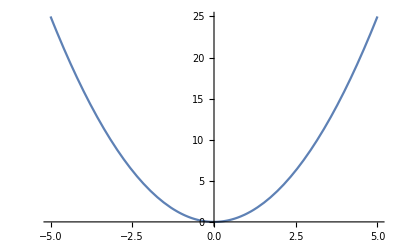

```mathematica
Plot[x^2,{x,-5,5}]
```

### Plotting Multiple Functions

Note the use of the brackets to make a list of functions.

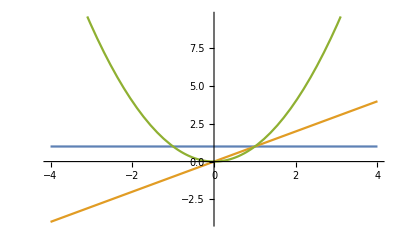

```mathematica
Plot[{1,x,x^2},{x,-4,4}]
```

### Prettying and Tidying Up Your Plot

This next part is likely overkill, but should have all the major syntax you’ll need to make a nice looking plot.

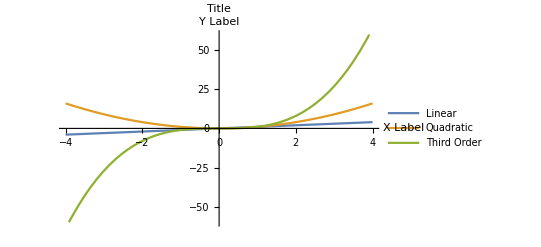

```mathematica
Plot[{x,x^2,x^3},{x,-4,4},PlotRange->{{-4,4},{-60,60}}, PlotLegends->{"Linear", "Quadratic","Third Order"},AxesLabel->{"X Label","Y Label"},PlotLabel->"Title"]
```

## Linear Algebra Basics

### Defining Matrices and Vectors

The syntax for vectors and matrices can be a bit confusing, so be careful when writing things out!

```mathematica
vec={{a},{b},{c}}; 
vec//MatrixForm
matrix={{a,b},{c,d}}; 
matrix//MatrixForm
```

(a
b
c)

(a | b
c | d)

Make sure you don’t include //MatrixForm when defining the matrix because I have run into some errors that way.  If you are using a vector for anything other than a basic dot product, make sure to use double brackets! Here are some issues:

```mathematica
badvec={a,b,c};
badvec//MatrixForm
Transpose[badvec]//MatrixForm
Transpose[vec]//MatrixForm
```

(a
b
c)

(a
b
c)

(a | b | c)

Notice how the last line gives the desired row vector while we can’t take the transpose of badvec.

There' s also a neat way to define large arrays that only have a few elements :

```mathematica
MatrixForm[SparseArray[{{3,3}->1, {2,1}->4,{5,1}->5,{1,5}->5}]]
```

(0 | 0 | 0 | 0 | 5
4 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
5 | 0 | 0 | 0 | 0)

If you don’t like the bracket form of inputting a matrix, check out this site https://reference.wolfram.com/language/howto/InputAMatrix.html and how you can input a matrix in MatrixForm.

### Matrix Multiplication

Now that we have our matrices, we can start to do fun things! (Note I define the other matrix like this by right clicking and then going to “Add Table/Matrix”)

```mathematica
matrix2 = ({{e, f}, {g, h}});
matrix matrix2 //MatrixForm
matrix.matrix2 //MatrixForm
```

(a e | b f
c g | d h)

(a e+b g | a f+b h
c e+d g | c f+d h)

Note the difference between the two products here. Without any symbols, each term is multiplied. With the “.”, Mathematica performs matrix multiplication.

### Matrix Functions

Besides regular matrix multiplication, here’s a bunch of useful functions you may need:

```mathematica
MatrixPower[matrix,2]//MatrixForm
MatrixPower[matrix,3]//MatrixForm
```

(a^2+b c | a b+b d
a c+c d | b c+d^2)

(a (a^2+b c)+b (a c+c d) | a (a b+b d)+b (b c+d^2)
c (a^2+b c)+d (a c+c d) | c (a b+b d)+d (b c+d^2))

```mathematica
Transpose[matrix]
```

{{a,c},{b,d}}

```mathematica
Det[matrix]
```

-b c+a d

```mathematica
Conjugate[matrix]//MatrixForm
ConjugateTranspose[matrix]//MatrixForm
```

(Conjugate[a] | Conjugate[b]
Conjugate[c] | Conjugate[d])

(Conjugate[a] | Conjugate[c]
Conjugate[b] | Conjugate[d])

```mathematica
Tr[matrix]
```

a+d

```mathematica
mat = {{0,1},{0,0}};
mat //MatrixForm
MatrixExp[mat]//MatrixForm
```

(0 | 1
0 | 0)

(1 | 1
0 | 1)

Here are some other useful functions to make standard matrices you’ll run into. This will save you some time if you don’t want to write out the full matrices yourself.

```mathematica
IdentityMatrix[2]//MatrixForm
IdentityMatrix[3]//MatrixForm
PauliMatrix[1]//MatrixForm
PauliMatrix[2]//MatrixForm
PauliMatrix[3]//MatrixForm
```

(1 | 0
0 | 1)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

(0 | 1
1 | 0)

(0 | -ⅈ
ⅈ | 0)

(1 | 0
0 | -1)

### Eigenvalues, Eigenvectors, etc

```mathematica
m = {{4,2},{-1,2}};
Eigenvalues[m]
Eigenvectors[m]
Eigensystem[m]//MatrixForm
```

{3+ⅈ,3-ⅈ}

{{-1-ⅈ,1},{-1+ⅈ,1}}

(3+ⅈ | 3-ⅈ
{-1-ⅈ,1} | {-1+ⅈ,1})

### Tensors

I personally dislike trying to use tensors in Mathematica and prefer the regular matrix representation. However there are some functions you can try out and see if you like:

```mathematica
TensorProduct[vec,vec]//MatrixForm
TensorSymmetry[TensorProduct[vec,vec]]
```

((a^2
a b
a c)
(a b
b^2
b c)
(a c
b c
c^2))

{{Cycles[{{1,3}}],1},{Cycles[{{2,4}}],1}}

```mathematica
Clear[x]
```

## Miscellaneous Useful Functions and Simplification Tricks

### Simplifying with Assumptions

A lot of the time, you’ll know more about the variables than Mathematica does. For example, the standard deviation in a Gaussian will be real and positive or you may only be looking at x>0.

```mathematica
Integrate[Exp[-x^2/(2 σ^2)],{x,-∞,∞}]
Refine[Integrate[Exp[-x^2/(2 σ^2)],{x,-∞,∞}],Assumptions->{σ ∈ Reals,σ > 0}]
```

ConditionalExpression[(√(2 π))/(√(1/σ^2)), Re[σ^2]>0]

√(2 π) σ

```mathematica
FullSimplify[√(x^2)]
FullSimplify[√(x^2),Assumptions->{x > 0}]
```

√(x^2)

x

This is especially useful for when you want to take the conjugate of things.

```mathematica
FullSimplify[(a+b I)Conjugate[a+b I]]
FullSimplify[(a+b I)Conjugate[a+b I],Assumptions->{{a,b} ∈ Reals}]
```

(a+ⅈ b) (Conjugate[a]-ⅈ Conjugate[b])

a^2+b^2

### TeXForm

This is incredibly useful if you LATEX your sets. You can take some massive expression and then get LATEX code that you can copy paste over.

```mathematica
TeXForm[(a x+b x^2+c x^3)/Exp[5 x^2]]
```

e^{-5 x^2} \left(a x+b x^2+c x^3\right)

```mathematica
TeXForm[matrix]
```

\left(
\begin{array}{cc}
 a & b \\
 c & d \\
\end{array}
\right)

This works with //TeXForm just like //MatrixForm

```mathematica
(a x+b x^2+c x^3)/Exp[5 x^2]//TeXForm
```

e^{-5 x^2} \left(a x+b x^2+c x^3\right)

### Units and Unit Simplifications

This is sometimes incredibly useful, but really only worth it if you want to solve a lot of the problem this way. Sometimes, it’s easier to just go to WolframAlpha instead. But here’s how you can do it in Mathematica.

```mathematica
Quantity[1,"Meters"]
```

1 m

```mathematica
Quantity[1,"Joules"]
```

1 J

```mathematica
Quantity[1,"Joules"]/Quantity[1,"Newtons"]
UnitSimplify[Quantity[1,"Joules"]/Quantity[1,"Newtons"]]
UnitConvert[Quantity[760,"MillimetersOfMercury0C"]]
UnitConvert[Quantity[760,"MillimetersOfMercury0C"],"Atmospheres"]
```

1 J/N

1 m

101325. kg/(m s^2)

0.999998 atm

Note that UnitConvert[] converts to base SI and is very useful.

Some other useful units to have: (note these all have the correct values and units if you use Unit

```mathematica
Quantity[1,"ReducedPlanckConstant"]
Quantity[1,"PlanckConstant"]
Quantity[1,"BoltzmannConstant"]
UnitConvert[Quantity[1,"BoltzmannConstant"]]
```

ℏ

h

k

1380649/100000000000000000000000000000 kg m^2/(s^2 K)

#### Delayed Evaluation

You can use the operator := (also known as the Walrus operator) to assign a value without actually evaluating it. Let’s see what this looks like.

```mathematica
c = 1;
f[x_] = c x^2;
g[x_] := c x^2;
f[x]
g[x]
```

x^2

x^2

Now let’s change the value of c.

```mathematica
c = 2;
f[x]
g[x]
```

x^2

2 x^2

Why did this happen? Well by delaying our evaluating with :=, we don’t know what g[x] is until we call it. However, f[x] is set to the function 1 x^2. So when we change c, g(x) doesn’t care since it doesn’t know c is even in the function while f(x) no longer has a c since it already let c=1. You should also look at the Evaluate[] function and how it forces immediate evaluation. Look at the differences in the plots:

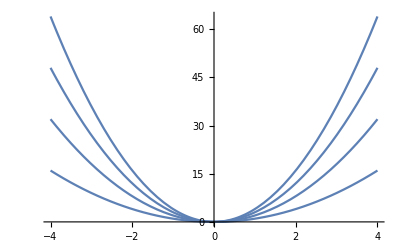

```mathematica
factors={1,2,3,4};
Plot[factors x^2,{x,-4,4}]
```

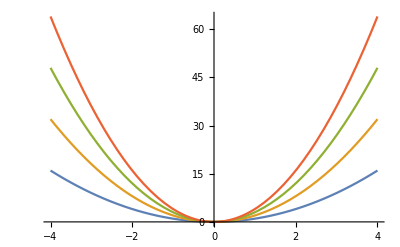

```mathematica
factors={1,2,3,4};
Plot[Evaluate[factors x^2],{x,-4,4}]
```

Notice the difference here . When we call Evaluate[], we make sure to get our list of values first, then plot . When we don' t evaluate, Mathematica thinks we have a single object and gives them all the same color . Calling Evaluate[] makes sure we have our list first that we can plot. You can also call functions using the @ symbol, so it may also be written as (this makes more sense if you want to do something like Evaluate[Table[]])

```mathematica
Plot[Evaluate@(factors x^2),{x,-4,4}]
```

-Graphics-